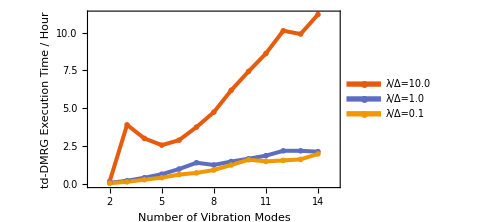

```mathematica
time01={767.4075922966003,1014.3099255561829,1478.566328048706,1904.334525346756,2555.9760699272156,2937.04980969429,3551.167452812195,4420.1347324848175,5381.642339468002};
time02={792.2276723384857,1194.6615300178528,1765.4887952804565,2399.117031812668,3518.0642478466034,4513.837941169739,4464.280539989471,5299.859427928925,5895.585768699646};
time03={1108.9923622608185,13916.076873540878,10555.395902395248,8834.623010873795,9418.066591978073,11963.920089006424,15840.023931980133,20140.584179639816,24868.209146738052};
t01={259.6982522,554.34344149,1074.89094591,1548.99136662,2282.787647252682,2682.74063826,3357.77400136,4560.3479352,5808.20631886,5416.49290776,5641.56569576,5887.84859586,7180.47377229};
t1={322.97051716,813.07363534,1530.26480937,2370.21997619
,3599.45760441,5095.07157707,4566.02108479,5380.39836979
,6040.82576871,6772.13242245,7924.37747097,7924.2224493
,7720.33188057};
t10={673.91125083,14084.87484598,10860.12617993,9269.17708015
,10455.01272726,13554.15199971,17100.34340692,22283.37200546
,26765.22690988,31013.82680368,36418.35504794,35641.44131708
,40279.30251431};
time[x_]:=Table[{i+1,x[[i]]/60/60},{i,1,Length[x]}];
runingTime=ListLinePlot[{time[t10],time[t1],time[t01]},
PlotRange->{{1,15},All},
FrameTicks->{Automatic,{Table[i,{i,2,14}],None}},
PlotStyle->Thickness[0.008],
PlotTheme->"Scientific",
PlotMarkers->"OpenMarkers",
GridLines->None,
LabelStyle->{FontFamily->"DejaVu Sans",12},
FrameStyle->Thickness[0.006],
PlotLegends->Placed[LineLegend[{"λ/Δ=10.0","λ/Δ=1.0","λ/Δ=0.1"},LegendFunction->None,LegendMargins-> -1,Spacings->{.1,0.0},LegendMarkerSize->15,LegendMargins->0,LegendLayout->{"Column",1}],{0.20,0.85}],
FrameLabel->{"Number of Vibration Modes","td-DMRG Execution Time / Hour"},ImageSize->Medium]
```

```mathematica
Export["runningTime.png",runingTime,ImageResolution->500]
```

runningTime.png

```mathematica
t01={259.6982522010803,554.3434414863586,1074.8909459114075,1548.9913666248322,2282.7876472473145,2682.740638256073,3357.7740013599396,4560.347935199738,5808.206318855286};
t1={322.9705171585083,813.0736353397369,1530.264809370041,2370.2199761867523,3599.457604408264,5095.071577072144,4566.021084785461,5380.3983697891235};
t10={673.9112508296967,14084.874845981598,10860.126179933548,9269.177080154419,10455.01272726059,13554.15199971199};
```

```mathematica
data={time[time01],time[time02],time[time03]};
timeFixedNumModes=Table[{0.1,data[[1,2]]},{i,1,}]
```